```mathematica
(*Use the method of Laplace transform for solving the following differential equation*)
```

-s+2 LaplaceTransform[y[t],t,s]+s^2 LaplaceTransform[y[t],t,s]+2 (-1+s LaplaceTransform[y[t],t,s])==ⅇ^(-π s)

{{LaplaceTransform[y[t],t,s]→(ⅇ^(-π s) (1+2 ⅇ^(π s)+ⅇ^(π s) s))/(2+2 s+s^2)}}

(ⅇ^(-π s) (1+2 ⅇ^(π s)+ⅇ^(π s) s))/(2+2 s+s^2)

1/2 ⅇ^((-1-ⅈ) t) ((1+ⅈ)+(1-ⅈ) ⅇ^(2 ⅈ t)+ⅈ ⅇ^π (-1+ⅇ^(2 ⅈ t)) HeavisideTheta[-π+t])

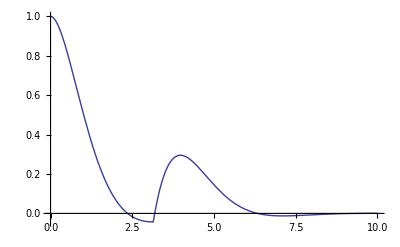

```mathematica
(*1*)
deq=y''[t]+2y'[t]+2y[t]==DiracDelta[t-Pi];
initial={y[0]->1,y'[0]->0};
aeq=LaplaceTransform[deq,t,s]/.initial
fs=Solve[aeq,LaplaceTransform[y[t],t,s]]
fs=LaplaceTransform[y[t],t,s]/.fs[[1]]/.w->1
yt=InverseLaplaceTransform[fs,s,t]
Plot[yt,{t,0,10}]
```

```mathematica
?Heavisidetheta
```

HeavisideTheta[x] represents the Heaviside theta function θ(x), equal to 0 for x<0 and 1 for x>0. 
HeavisideTheta[x_1,x_2,…] represents the multidimensional Heaviside theta function which is 1 only if none of the x_i are not positive.

```mathematica
deq=y''[x]+y'[x]+y[x]Log[1+x]==0;
initial={y[0]->1,y'[0]->0};
aeq=LaplaceTransform[deq,x,s]/.initial;
fs=Solve[aeq,LaplaceTransform[y[x],x,s]]
fs=LaplaceTransform[y[x],x,s]/.fs[[1]]/.w->1
yt=InverseLaplaceTransform[fs,s,x]
Plot[yt,{x,0,10}]
```

{{LaplaceTransform[y[x],x,s]→(1+s-LaplaceTransform[Log[1+x] y[x],x,s])/(s (1+s))}}

(1+s-LaplaceTransform[Log[1+x] y[x],x,s])/(s (1+s))

Series approximation

Comapare exact solution and series approximation

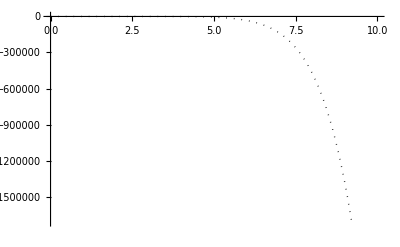

```mathematica
deq=y''[x]+y'[x]+Log[1+x] y[x]==0;
initial={y[0]==1,y'[0]==0};s=10;
ser=y[x]+O[x]^s;
sereq=deq/.{y[x]->ser,y'[x]->D[ser,x],y''[x]->D[ser,{x,2}]};
(*Make the list of equations*)
eqs=Join[{sereq},initial];
unknowns=Table[Derivative[n][y][0],{n,0,s-1}];
knowns=Solve[eqs,unknowns];
ser=ser/.knowns[[1]];
"Series approximation"
sersol=Normal[ser];
(*Exact solution*)
(*sol1=DSolve[{deq,y[0]==1,y'[0]==0},y[x],x];
"Exact solution"
exsol=y[x]/.sol1[[1]]*)
"Comapare exact solution and series approximation"
Plot[sersol,{x,0,10},PlotStyle->{{Black,Thick,Dotted}}]
```